```mathematica
f[t_]:=Exp[-t]*Sin[20*t]
```

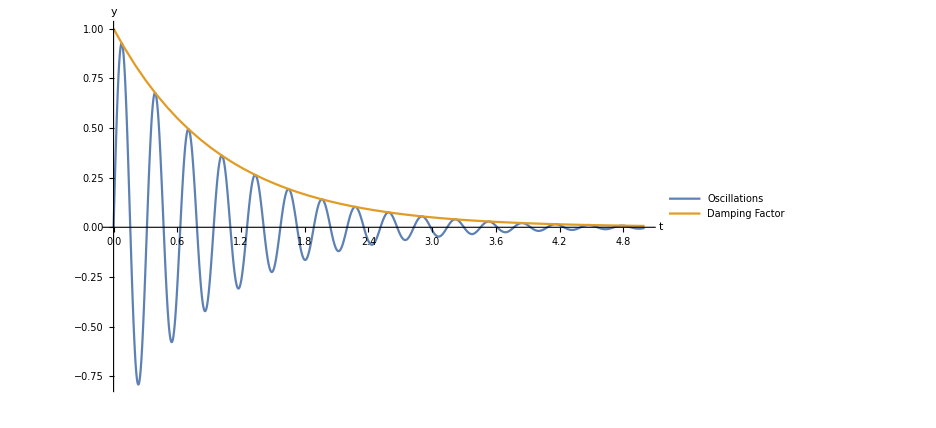

```mathematica
Plot[{f[x],Exp[-x]},{x,0,5},PlotLegends->Placed[LineLegend[{"Oscillations","Damping Factor"},LegendFunction->Frame],{0.9,0.9}],PlotRange->All,AxesLabel->{t,y}]
```